```mathematica
(* custom eigensystem *)
Clear[orderedEigensystem]
orderedEigensystem[M_,f_:Re]:=Module[{eigsys, order},
eigsys = Eigensystem[M];
order = Ordering[f[eigsys[[1]]]];
{eigsys[[1,order]],eigsys[[2,order]]ᵀ}
];

Clear[orderedGaugedEigensystem]
orderedGaugedEigensystem[M_,f_:Re]:=Module[{vals,vecs, order,phase},
{vals,vecs} = Eigensystem[M];
order = Ordering[f[vals]];
vals=vals[[order]];
vecs=vecs[[order]];
phase = AbsArg[vecs[[1,1]]][[2]];
If[phase≠Mod[phase,π/2],vecs*=ⅈ];
vecs=vecsᵀ;
{vals,vecs}
];

(* compute density of states *)
Clear[DOS]
DOS[E_,NE_]:=Module[{min,max,Eints,dos},
{min,max}=MinMax[E];
Eints =min+ Table[(max-min)/NE n,{n,0,NE}];
dos=Table[Length[Nearest[E,e,{Infinity,(max-min)/(2*NE)}]],{e,Eints}];
(*Print[Eints,Length[E]];*)
{Eints,dos/Length[E]}ᵀ
];

(* convenient matrices to define the BBH model *)
Clear[λ,γ,Δ,L,ks,kxs,kys,tp,bands, Γ,h,spec,spec2,ϵ,ϵ2]
Γ[0]=PauliMatrix[3]⊗PauliMatrix[0]//ArrayFlatten;
Table[Γ[k]=PauliMatrix[2]⊗PauliMatrix[k]//ArrayFlatten,{k,1,3}];
Γ[4]=PauliMatrix[1]⊗PauliMatrix[0]//ArrayFlatten;

(* BBH hamiltonian, spectrum & modes *)
h[kx_,ky_,γx_,γy_,λx_,λy_,Δ_,ϕ_]:=(γx+λx Cos[kx])Γ[4]+λx Cos[kx+ϕ]Γ[3]+(γy+λy Cos[ky])Γ[2]+λy Cos[ky+ϕ]Γ[1]+Δ Γ[0];
ϵ[kx_,ky_,γx_,γy_,λx_,λy_,Δ_,ϕ_]:=orderedEigensystem[N[h[kx,ky,γx,γy,λx,λy,Δ,ϕ]]];
spec[γx_,γy_,λx_,λy_,Δ_,ϕ_,kx_,ky_]:={kx,ky,ϵ[kx,ky,γx,γy,λx,λy,Δ,ϕ]}
```

0.616361

-Graphics3D-

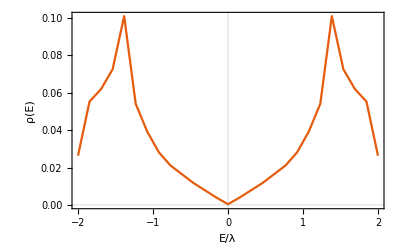

0.649806

-Graphics3D-

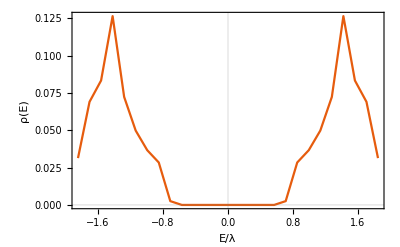

0.636944

-Graphics3D-

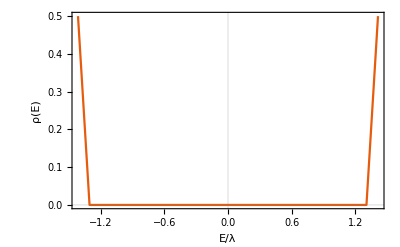

```mathematica
ϵ2[kx_,ky_,γx_,γy_,λx_,λy_,Δ_,ϕ_]:=orderedGaugedEigensystem[N[h[kx,ky,γx,γy,λx,λy,Δ,ϕ]]];
spec2[γx_,γy_,λx_,λy_,Δ_,ϕ_,kx_,ky_]:={kx,ky,ϵ2[kx,ky,γx,γy,λx,λy,Δ,ϕ]}

Lx=Ly=100;(* momentum space discretization *)
NE=If[OddQ[Lx/4],Lx/4+1,Lx/4]; (* discretization of the DOS *)
kxs = Table[N[(2π)/Lx n-π],{n,0,Lx}];
kys = Table[N[(2π)/Ly n]-π,{n,0,Ly}];

(* ϕ = 0, bulk gap closing *)
AbsoluteTiming[res =Table[spec[0.,0.,1.,1.,0.0,0 π/4,kx,ky],{kx,kxs},{ky,kys}];][[1]]
bands=Table[Flatten[Table[Join[res[[i,j,;;2]],{res[[i,j,3,1,b]]}], {i,Length[kxs]},{j,Length[kys]}],1],{b,Length[res[[1,1,3,1]]]}];
ListPlot3D[bands,MaxPlotPoints->Automatic,InterpolationOrder->1,Mesh->None, AxesLabel->{"k_x","k_y","E/λ"},PlotTheme->"Scientific"]
dos=DOS[Flatten[bands[[;;,;;,3]]],NE];
ListPlot[dos,FrameLabel->{"E/λ","ρ(E)"},Joined->True,PlotTheme->"Scientific"]

(* ϕ = π/4, bulk gap is finite *)
AbsoluteTiming[res =Table[spec[0.,0.,1.,1.,0.0,π/4,kx,ky],{kx,kxs},{ky,kys}];][[1]]
bands=Table[Flatten[Table[Join[res[[i,j,;;2]],{res[[i,j,3,1,b]]}], {i,Length[kxs]},{j,Length[kys]}],1],{b,Length[res[[1,1,3,1]]]}];
ListPlot3D[bands,MaxPlotPoints->Automatic,InterpolationOrder->1,Mesh->None, AxesLabel->{"k_x","k_y","E/λ"},PlotTheme->"Scientific"]
dos=DOS[Flatten[bands[[;;,;;,3]]],NE];
ListPlot[dos,FrameLabel->{"E/λ","ρ(E)"},Joined->True,PlotTheme->"Scientific"]

(* ϕ = π/2, bulk gap maximal *)
AbsoluteTiming[res =Table[spec[0.,0.,1.,1.,0.0,π/2,kx,ky],{kx,kxs},{ky,kys}];][[1]]
bands=Table[Flatten[Table[Join[res[[i,j,;;2]],{res[[i,j,3,1,b]]}], {i,Length[kxs]},{j,Length[kys]}],1],{b,Length[res[[1,1,3,1]]]}];
ListPlot3D[bands,MaxPlotPoints->Automatic,InterpolationOrder->1,Mesh->None, AxesLabel->{"k_x","k_y","E/λ"},PlotTheme->"Scientific"]
dos=DOS[Flatten[bands[[;;,;;,3]]],NE];
ListPlot[dos,FrameLabel->{"E/λ","ρ(E)"},Joined->True,PlotTheme->"Scientific"]
```

```mathematica
Lx=Ly=100;(* momentum space discretization *)
NE=If[OddQ[Lx/4],Lx/4+1,Lx/4]; (* discretization of the DOS *)
kxs = Table[N[(2π)/Lx n-π],{n,0,Lx-1}];
kys = Table[N[(2π)/Ly n-π],{n,0,Ly-1}];
```

0.622299

-Graphics3D-

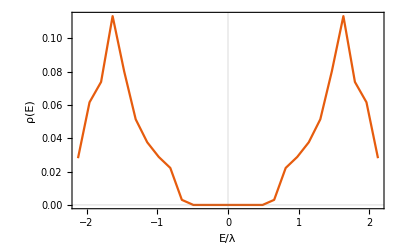

```mathematica
AbsoluteTiming[res =Table[spec[0.5,0.5,1.0,1.0,0.0,π/2,kx,ky],{kx,kxs},{ky,kys}];][[1]]
bands=Table[Flatten[Table[Join[res[[i,j,;;2]],{res[[i,j,3,1,b]]}], {i,Length[kxs]},{j,Length[kys]}],1],{b,Length[res[[1,1,3,1]]]}];
ListPlot3D[bands,MaxPlotPoints->Automatic,InterpolationOrder->1,Mesh->None, AxesLabel->{"k_x","k_y","E/λ"},PlotTheme->"Scientific"]
dos=DOS[Flatten[bands[[;;,;;,3]]],NE];
ListPlot[dos,FrameLabel->{"E/λ","ρ(E)"},Joined->True,PlotTheme->"Scientific"]
```

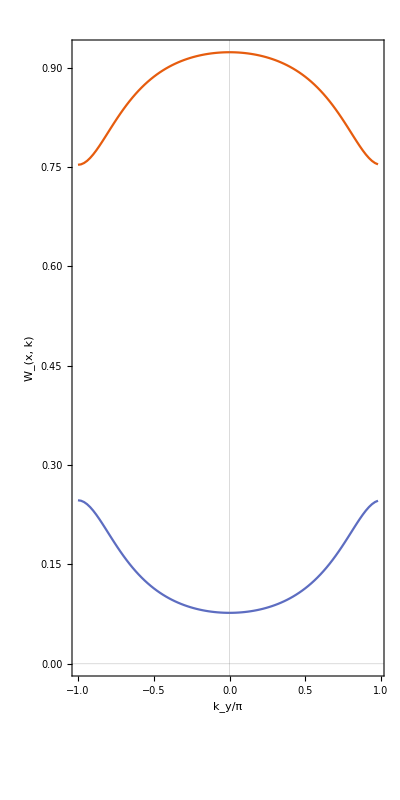

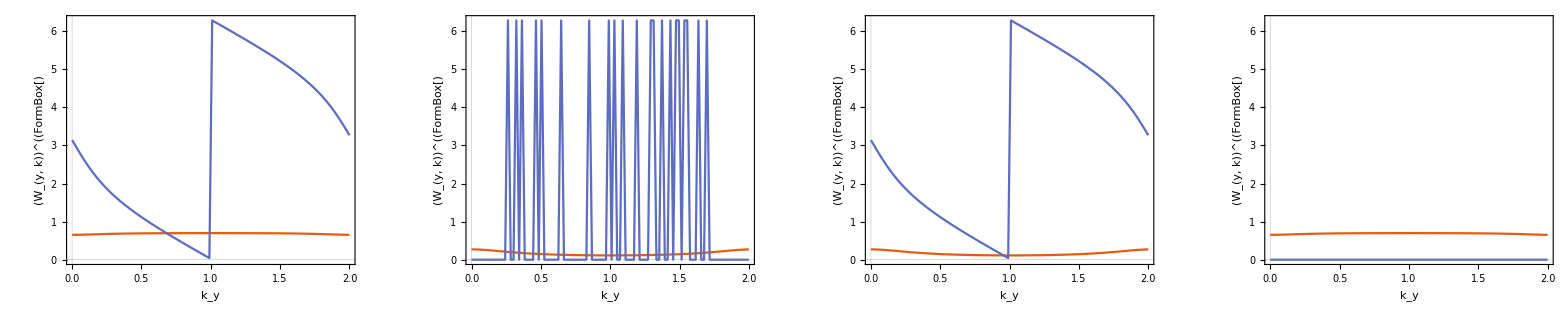

{0.5,0.5}

```mathematica
Clear[Fk,Norb,x,y,Fx,u,ux,Fx]
Norb=2;
Wtilde={};
Wx = ConstantArray[0,{Lx,Ly,2,2}];
Do[
Wxy={};
Vxy={};
Axy={};
Do[
Fxy = IdentityMatrix[Norb];
phase=1;
Do[
u=res[[Mod[x+xp-1,Lx]+1,y,3,2,;;,;;Norb]];
ux=res[[Mod[x+xp,Lx]+1,y,3,2,;;,;;Norb]];
prod = ux†.u;
Fxy=prod.Fxy;
Fxy/=Norm[Fxy]; (* this might stabilize *)
,{x,1,Length[res]}];
{vals,vecs} = orderedEigensystem[Fxy,Im];
AppendTo[Wxy,Table[Mod[Arg[e]/(2π),1],{e,vals}]];
AppendTo[Axy,Table[Abs[e],{e,vals}]];
vs=res[[Mod[xp,Lx]+1,y,3,2,;;,;;Norb]].vecs;
AppendTo[Vxy,vs];
Wx[[xp+1,y]]=prod;
,{y,1,Length[res[[1]]]}];
AppendTo[Wtilde,Eigenvalues[Chop[Product[Vxy[[Mod[n,Ly]+1]]†.Vxy[[n]],{n,Ly}]]]];
,{xp,{0.0}}]
ListPlot[Wxyᵀ,PlotRange->Full,Joined->True,PlotTheme->"Scientific",DataRange->MinMax[kys]/π,FrameLabel->{"k_y/π","W_(x, k)"},AspectRatio->2]
GraphicsRow[Table[ListPlot[Mod[AbsArg[Vxy[[;;,n]]][[;;,2]]ᵀ,2π],PlotRange->{{0,2},{0,2π}},Joined->True,DataRange->{0,2},PlotTheme->"Scientific",FrameLabel->{"k_y",StringForm["(W_(y, k))^(`1`)",n]}],{n,4}],ImageSize->2000]
py=Mean[Mod[Im[Log[Wtilde]],2π]]/(2π) (* polarization == 0.0, if |γ| > |λ| (triv. phase) *)
```

```mathematica
{vals,vecs}=orderedEigensystem[Fxy]
```

{{0.024446+0.999701 ⅈ,0.024446-0.999701 ⅈ},{{0.924255+0. ⅈ,0.381028-0.0238778 ⅈ},{-0.381028-0.0238778 ⅈ,0.924255+0. ⅈ}}}

```mathematica
vals
```

{0.024446+0.999701 ⅈ,0.024446-0.999701 ⅈ}

```mathematica
Mod[Arg[vals]/(2π),1]
```

```mathematica
Abs[vals]*Exp[ⅈ 2π*Mod[Arg[vals]/(2π),1]]
```

{0.024446+0.999701 ⅈ,0.024446-0.999701 ⅈ}

```mathematica
vecs†.Fxy.vecs
```

{{0.024446+0.999701 ⅈ,-8.43076×10^-16+9.4369×10^-16 ⅈ},{-8.1532×10^-16-1.16573×10^-15 ⅈ,0.024446-0.999701 ⅈ}}

```mathematica
vals
```

{0.024446+0.999701 ⅈ,0.024446-0.999701 ⅈ}

```mathematica
Chop[ⅈ vecs.DiagonalMatrix[Log[Mod[Arg[vals]/(2π),1]]].vecs†]//MatrixForm
```

(0.-1.23882 ⅈ | 0.0247059+0.394242 ⅈ
-0.0247059+0.394242 ⅈ | 0.-0.445673 ⅈ)

```mathematica
mx = ArrayFlatten[PauliMatrix[1]⊗PauliMatrix[3]];
my = ArrayFlatten[PauliMatrix[1]⊗PauliMatrix[1]];
```

```mathematica
h[kx,ky,γ,λ,0,ϕ]//MatrixForm
```

```mathematica
v[kx_,ky_,γ_,λ_,ϕ_]=h[kx,ky,γ,λ,0,ϕ][[1;;2,3;;4]]//FullSimplify
%//MatrixForm
h[kx,ky,0,1,0,π/2]//FullSimplify//MatrixForm
v[kx,ky,0,1,π/2]//FullSimplify//MatrixForm
```

```mathematica
{vals,vecs}=orderedEigensystem[h[kx,ky,0,1,0,π/2]];
ComplexExpand[Table[vecs[[;;,j]]=Normalize[vecs[[;;,j]]],{j,Length[vecs]}]]//FullSimplify
Chop[vecs/.{kx->kxs[[2]],ky->0.}]//N
Chop[res[[2,1,3,2]]]
```

```mathematica
(Chop[vecs/.{kx->kxs[[2]],ky->0.}])†.res[[2,1,3,2]]
Chop[%]//MatrixForm
```

```mathematica
FullSimplify[ComplexExpand[vecs[[;;,;;2]]†.D[vecs[[;;,;;2]],ky]]/.{kx->0,ky->0}]
AbsArg[Eigenvalues[%]]
```

```mathematica
res[[1,1,3,2]]†.(res[[2,1,3,2]]-res[[1,1,3,2]])
AbsArg[Eigenvalues[%]]
```

```mathematica
Γ[0].h[kx,ky,γ,λ,Δ,ϕ]+h[kx,ky,γ,λ,Δ,ϕ].Γ[0]//MatrixForm
Γ[0]//MatrixForm
```

```mathematica
(* double FT *)
Lx=Ly=14;
Clear[δ,Hrs,γ,λ,Δ];
(h[kx,ky,γx,γy,λx,λy,Δ,ϕ]*Exp[ⅈ*{kx,ky}.({x1,y1}-{x2,y2})]//TrigToExp//ExpandAll)/.{ⅇ^(ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)->δ[x1,x2]*δ[y1,y2],ⅇ^(-ⅈ kx+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)->δ[x1,x2+1]*δ[y1,y2],ⅇ^(ⅈ kx+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)-> δ[x1+1,x2]*δ[y1,y2],ⅇ^(-ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)-> δ[x1,x2]*δ[y1,y2+1],ⅇ^(ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2)-> δ[x1,x2]*δ[y1+1,y2],ⅇ^(-ⅈ kx+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2-ⅈ ϕ)-> ⅇ^(-ⅈ ϕ)δ[x1,x2+1]δ[y1,y2],ⅇ^(ⅈ kx+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2+ⅈ ϕ)-> ⅇ^(+ⅈ ϕ)δ[x1+1,x2]δ[y1,y2], ⅇ^(-ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2-ⅈ ϕ)-> ⅇ^(-ⅈ ϕ)δ[x1,x2]δ[y1,y2+1],ⅇ^(ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2+ⅈ ϕ)->ⅇ^(+ⅈ ϕ)δ[x1,x2]δ[y1+1,y2],ⅇ^(ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2-ⅈ ϕ)->ⅇ^(-ⅈ ϕ)δ[x1,x2]δ[y1+1,y2],ⅇ^(-ⅈ ky+ⅈ kx x1-ⅈ kx x2+ⅈ ky y1-ⅈ ky y2+ⅈ ϕ)->ⅇ^(+ⅈ ϕ)δ[x1,x2]δ[y1,y2+1]};
(* assign local real space Hamiltonian *)
Hrs[x1_,x2_,y1_,y2_]=%;
δ[x_,y_]=If[x==y,1,0];
(* now construct the full one *)
Clear[Hfull];
pbc=False;
Hfull= ConstantArray[0,{Lx,Ly,Length[Hrs[1,1,1,1]],Lx,Ly,Length[Hrs[1,1,1,1]]}];
Do[
If[x1>0&&x1≤Lx&&y2>0&&y2≤Ly,
Hfull[[x1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];

(* the boundary terms *)
If[x1==Lx+1&&y2>0&&y2≤Ly&&pbc,
Hfull[[1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];
If[y2==Ly+1&&x1>0&&x1≤Lx&&pbc,
Hfull[[x1,y1,;;,x2,1,;;]]+=Hrs[x1,x2,y1,y2];
];

If[x1==0&&y2>0&&y2≤Ly&&pbc,
Hfull[[Lx,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];
If[y2==0&&x1>0&&x1≤Lx&&pbc,
Hfull[[x1,y1,;;,x2,Ly,;;]]+=Hrs[x1,x2,y1,y2];
];
,{x1,x2-1,x2+1},{x2,Lx},{y1,Ly},{y2,y1-1,y1+1}];
Hmat=ArrayReshape[Hfull,{Lx*Ly*4,Lx*Ly*4}];
```

```mathematica
L=Lx;(* momentum space discretization *)
ks = Table[N[(2π)/L n-π],{n,0,L}];
γs=Range[-2,2,0.1];
phi=0.5π;
bands={};
modes={};
bandsPBC={};
Monitor[
Do[
(*res = orderedEigensystem[N[(Hmat/.{γx->0.5,γy->g,λx->1.0,λy->1.0,Δ->0.0,ϕ->phi})]];*)
res = Sort[Eigenvalues[N[(Hmat/.{γx->1.5,γy->g,λx->1.0,λy->1.0,Δ->0.0,ϕ->phi})]]];
AppendTo[bands,res];
(*AppendTo[modes,res[[2]]];*)
res =Table[spec[1.5,g,1.,1.,0.,phi,kxs,kys],{kxs,ks},{kys,ks}];
AppendTo[bandsPBC,Flatten[res[[;;,;;,3,1]]]];
,{g,γs}]
,g]
```

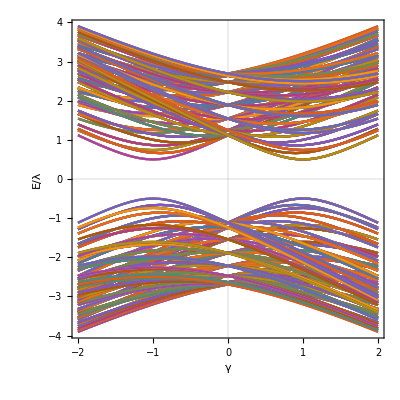

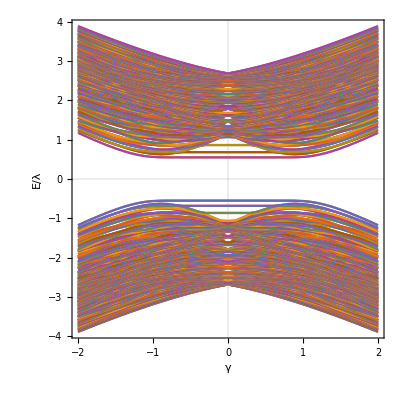

```mathematica
(* first plot PBC bands *)
plotPBC=ListPlot[Sort[Re[bandsPBC]ᵀ],DataRange->MinMax[γs],Joined->True,FrameLabel->{"γ","E/λ"},PlotTheme->"Scientific",AspectRatio->1]
(* compare with OBC bands *)
Show[ListPlot[bandsᵀ,DataRange->MinMax[γs],Joined->True,FrameLabel->{"γ","E/λ"},PlotTheme->"Scientific",AspectRatio->1]]
```

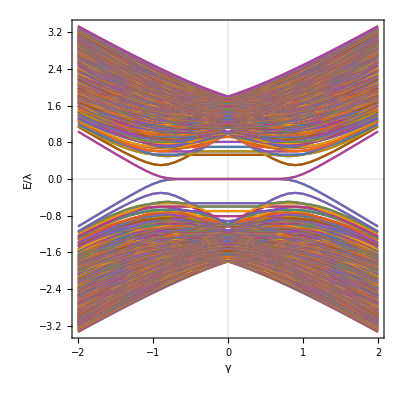

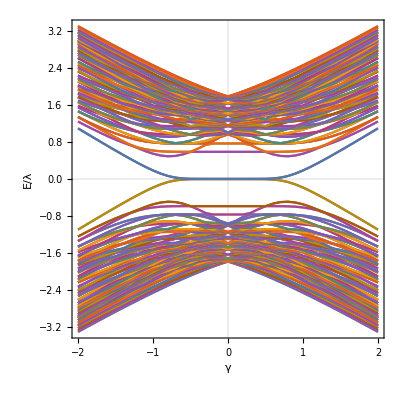

```mathematica
Chop[bands][[(Length[bands]-1)/2]]
```

```mathematica
0.5,1.5
```

```mathematica
res = Chop[orderedEigensystem[N[(Hmat/.{γx->0.5,γy->1.5,λx->1.0,λy->1.0,Δ->0.0,ϕ->π/2})]]];
res[[1]]
```

{-2.86912,-2.86912,-2.83383,-2.83383,-2.77951,-2.77951,-2.76854,-2.76854,-2.73196,-2.73196,-2.71267,-2.71267,-2.67557,-2.67557,-2.64187,-2.64187,-2.60867,-2.60867,-2.60606,-2.60606,-2.57712,-2.57712,-2.56981,-2.56981,-2.53229,-2.53229,-2.52921,-2.52921,-2.50978,-2.50978,-2.46466,-2.46466,-2.4601,-2.4601,-2.43554,-2.43554,-2.41452,-2.41452,-2.40179,-2.40179,-2.35952,-2.35952,-2.35644,-2.35644,-2.34203,-2.34203,-2.294,-2.294,-2.28361,-2.28361,-2.2294,-2.2294,-2.21253,-2.21253,-2.16667,-2.16667,-2.15067,-2.15067,-2.12514,-2.12514,-2.11972,-2.11972,-2.04653,-2.04653,-2.04409,-2.04409,-1.98334,-1.98334,-1.95478,-1.95478,-1.93028,-1.93028,-1.89442,-1.89442,-1.87743,-1.87743,-1.85529,-1.85529,-1.79439,-1.79439,-1.76186,-1.76186,-1.72864,-1.72864,-1.69101,-1.69101,-1.689,-1.689,-1.66942,-1.66942,-1.59966,-1.59966,-1.58579,-1.58579,-1.57546,-1.57546,-1.57278,-1.57278,-1.53548,-1.53548,-1.46141,-1.46141,-1.45428,-1.45428,-1.43275,-1.43275,-1.37516,-1.37516,-1.31752,-1.31752,-1.29832,-1.29832,-1.24348,-1.24348,-1.18234,-1.18234,-1.14305,-1.14305,-1.07391,-1.07391,-0.984194,-0.984194,-0.899151,-0.899151,-0.850879,-0.850879,-0.615781,-0.615781,0.615781,0.615781,0.850879,0.850879,0.899151,0.899151,0.984194,0.984194,1.07391,1.07391,1.14305,1.14305,1.18234,1.18234,1.24348,1.24348,1.29832,1.29832,1.31752,1.31752,1.37516,1.37516,1.43275,1.43275,1.45428,1.45428,1.46141,1.46141,1.53548,1.53548,1.57278,1.57278,1.57546,1.57546,1.58579,1.58579,1.59966,1.59966,1.66942,1.66942,1.689,1.689,1.69101,1.69101,1.72864,1.72864,1.76186,1.76186,1.79439,1.79439,1.85529,1.85529,1.87743,1.87743,1.89442,1.89442,1.93028,1.93028,1.95478,1.95478,1.98334,1.98334,2.04409,2.04409,2.04653,2.04653,2.11972,2.11972,2.12514,2.12514,2.15067,2.15067,2.16667,2.16667,2.21253,2.21253,2.2294,2.2294,2.28361,2.28361,2.294,2.294,2.34203,2.34203,2.35644,2.35644,2.35952,2.35952,2.40179,2.40179,2.41452,2.41452,2.43554,2.43554,2.4601,2.4601,2.46466,2.46466,2.50978,2.50978,2.52921,2.52921,2.53229,2.53229,2.56981,2.56981,2.57712,2.57712,2.60606,2.60606,2.60867,2.60867,2.64187,2.64187,2.67557,2.67557,2.71267,2.71267,2.73196,2.73196,2.76854,2.76854,2.77951,2.77951,2.83383,2.83383,2.86912,2.86912}

```mathematica
Dimensions[res[[2]]]
```

```mathematica
Lx=8
```

```mathematica
Abs[Chop[res[[2,;;,2Lx*Lx-1]]]]^2
```

```mathematica
{0,0,0.
,0,0,0.0048559614730777,0,0,0,0,0.07808901253370998,0,0,0.018636494831701683,0,0,0,0,0.037213227947488485,0,0,0.03910720888149641,0,0,0,0,0.009696351316797615,0,0,0.06294895899829407,0,0,0.00484042402679488,0,0,0,0,0,0,2.6369251783744875*^-9,0.003007126352891888,0,0,0,0,0,0,1.0120146696147062*^-8,0.001433042560100984,0,0,0,0,0,0,2.1236326590997973*^-8,0.00037339636685830693,0,0,0,0,0,0,3.418307493901758*^-8,0,0,0.07808901253370985,0,0,0.0030167790328875094,0,0,0,0,0.04851300757155244,0,0,0.011577972182542947,0,0,0,0,0.02311881723948146,0,0,0.024295457952568145,0,0,0,0,0.006023884149452797,0,0,0.03910720888149637,0,0,0.018576864305604457,0,0,0,0,0,0,1.0120146696140707*^-8,0.011540926558963056,0,0,0,0,0,0,3.8839694804911075*^-8,0.005499815106235577,0,0,0,0,0,0,8.150202446029585*^-8,0.001433042560100994,0,0,0,0,0,0,1.311898174983717*^-7,0,0,0.03721322794748853,0,0,0.001437642533507305,0,0,0,0,0.023118817239481466,0,0,0.005517469154993584,0,0,0,0,0.011017245421534306,0,0,0.011577972182542917,0,0,0,0,0.002870674973461591,0,0,0.01863649483170169,0,0,0.038982078943659036,0,0,0,0,0,0,2.1236326591000143*^-8,0.024217720644529976,0,0,0,0,0,0,8.150202446047553*^-8,0.011540926558963027,0,0,0,0,0,0,1.7102554550201608*^-7,0.0030071263528918942,0,0,0,0,0,0,2.7529144521917314*^-7,0,0,0.009696351316797603,0,0,0.00037459494490852654,0,0,0,0,0.006023884149452778,0,0,0.0014376425335073002,0,0,0,0,0.002870674973461571,0,0,0.0030167790328874916,0,0,0,0,0.0007479886748416559,0,0,0.0048559614730777,0,0,0.06274754346515668,0,0,0,0,0,0,3.418307493897617*^-8,0.03898207894365905,0,0,0,0,0,0,1.3118981749840162*^-7,0.018576864305604478,0,0,0,0,0,0,2.7529144521875385*^-7,0.0048404240267948895,0,0,0,0,0,0,4.431231579369829*^-7}
```

```mathematica
(* plot modes *)
modesReshaped=Table[ArrayReshape[modes[[i,;;,j]],{Lx,Ly,4}],{i,Length[modes]},{j,Length[modes[[1,1]]]}];
Manipulate[GraphicsRow[Table[ListPlot3D[Flatten[Table[{lx,ly,Abs[modesReshaped[[i,j,lx,ly,b]]]},{lx,Lx},{ly,Ly}],1],PlotRange->Full,Mesh->None,PlotTheme->"Scientific",AxesLabel->{"x","y",StringForm["(ψ_(`1`))^*ψ_(`1`)",b]}],{b,1,Length[modesReshaped[[i,j,1,1]]]}]],{{i,Floor[Length[modesReshaped]/2]},1,Length[modesReshaped],1},{{j,Floor[Length[modesReshaped[[1]]]/2]},1,Length[modesReshaped[[1]]],1}]
```

```mathematica
(* x-direction finite, periodic along y *)
Clear[δ,Hmixed,γ,λ,Δ];
γs=Range[-2,2,0.1];
(h[kx,ky,γ,λ,Δ,phi]*Exp[ⅈ*{kx,0}.({x1,y1}-{x2,y2})]//TrigToExp//ExpandAll)/.{ⅇ^(ⅈ kx x1-ⅈ kx x2)->δ[x1,x2],ⅇ^(-ⅈ kx+ⅈ kx x1-ⅈ kx x2) -> δ[x1,x2+1],ⅇ^(ⅈ ky+ⅈ kx x1-ⅈ kx x2)->δ[x1,x2] ⅇ^(ⅈ ky),ⅇ^(-ⅈ ky+ⅈ kx x1-ⅈ kx x2)->ⅇ^(-ⅈ ky)δ[x1,x2],ⅇ^(ⅈ kx+ⅈ kx x1-ⅈ kx x2)->δ[x1+1,x2]};
(* assign local real space Hamiltonian *)
Hmixed[x1_,x2_,ky_]=%;
δ[x_,y_]=If[x==y,1,0];
(* now construct the full one *)
Clear[Hfull];
pbc=False;
Hfull= ConstantArray[0,{Lx,Length[Hmixed[1,1,1]],Lx,Length[Hmixed[1,1,1]]}];
Do[
If[x1>0&&x1≤Lx,
Hfull[[x1,;;,x2,;;]]+=Hmixed[x1,x2,ky];
];

(* the boundary terms *)
If[x1==Lx+1&&pbc,
Hfull[[1,;;,x2,;;]]+=Hmixed[x1,x2,ky];
];

If[x1==0&&pbc,
Hfull[[Lx,;;,x2,;;]]+=Hmixed[x1,x2,ky];
];
,{x1,x2-2,x2+2},{x2,Lx}];
Hmat=ArrayReshape[Hfull,{Lx*4,Lx*4}];
ks = Table[N[(2π)/Ly n-π],{n,0,Ly}];
ListPlot[Table[Sort[Eigenvalues[Hmat/.{ky->k,γ->0.,λ->1,Δ->0.}]],{k,ks}]ᵀ,DataRange->MinMax[ks]/π,Joined->True,PlotTheme->"Scientific",FrameLabel->{"k_y","E/λ"}]
```

```mathematica
(* y-direction finite, periodic along x *)
Clear[δ,Hmixed,γ,λ,Δ];
γs=Range[-2,2,0.1];
(h[kx,ky,γ,λ,Δ,phi]*Exp[ⅈ*{0,ky}.({x1,y1}-{x2,y2})]//TrigToExp//ExpandAll)/.{ⅇ^(ⅈ ky y1-ⅈ ky y2)->δ[y1,y2],ⅇ^(-ⅈ kx+ⅈ ky y1-ⅈ ky y2) -> ⅇ^(-ⅈ kx)δ[y1,y2],ⅇ^(ⅈ ky+ⅈ ky y1-ⅈ ky y2)->δ[y1+1,y2],ⅇ^(-ⅈ ky+ⅈ ky y1-ⅈ ky y2)->δ[y1,y2+1],ⅇ^(ⅈ kx+ⅈ ky y1-ⅈ ky y2)->ⅇ^(ⅈ kx)δ[y1,y2]};
(* assign local real space Hamiltonian *)
Hmixed[y1_,y2_,kx_]=%;
δ[x_,y_]=If[x==y,1,0];
(* now construct the full one *)
Clear[Hfull];
pbc=False;
Hfull= ConstantArray[0,{Lx,Length[Hmixed[1,1,1,1]],Lx,Length[Hmixed[1,1,1,1]]}];
Do[
If[y2>0&&y2≤Ly,
Hfull[[y1,;;,y2,;;]]+=Hmixed[y1,y2,kx];
];

(* the boundary terms *)
If[y2==Ly+1&&pbc,
Hfull[[y1,;;,1,;;]]+=Hmixed[y1,y2,kx];
];
If[y2==0&&pbc,
Hfull[[y1,;;,Ly,;;]]+=Hmixed[y1,y2,kx];
];
,{y1,Ly},{y2,y1-1,y1+1}];
Hmat=ArrayReshape[Hfull,{Ly*4,Ly*4}];
ks = Table[N[(2π)/Lx n-π],{n,0,Lx}];
res = Table[orderedEigensystem[Hmat/.{kx->k,γ->0.,λ->1,Δ->0.}],{k,ks}];
ListPlot[res[[;;,1]]ᵀ,DataRange->MinMax[ks]/π,Joined->True,PlotTheme->"Scientific",FrameLabel->{"k_x","E/λ"}]
```

```mathematica
modesReshaped=Table[ArrayReshape[res[[i,2,;;,j]],{Lx,4}],{i,Length[res]},{j,Length[res[[1,2,1]]]}];
Manipulate[GraphicsRow[Table[ListPlot[Table[{lx,Abs[modesReshaped[[i,j,lx,b]]]},{lx,Lx}],PlotRange->Full,Mesh->None,PlotTheme->"Scientific",Joined->True,FrameLabel->{"x",StringForm["ψ_(`1`)(k_(`2`))^*ψ_(`1`)(k_(`2`))",b,i]}],{b,1,Length[modesReshaped[[i,1,1]]]}]],{{i,Floor[Length[modesReshaped]/2]},1,Length[modesReshaped],1},{{j,Floor[Length[modesReshaped[[1]]]/2]},1,Length[modesReshaped[[1]]],1}]
```

```mathematica
Clear[h,Δ,kx,ky,H,Δuu,Δud,Δdu,Δdd]
ξ[kx_,ky_]=(1-Cos[kx]-Cos[ky]);
h[kx_,ky_]=ξ[kx,ky]*PauliMatrix[0]+
{bx,by,bz}.Table[PauliMatrix[i],{i,3}];
h2[kx_,ky_]=-PauliMatrix[3].h[kx,ky]*.PauliMatrix[3];


Δuu[kx_,ky_]=+(Sin[kx]-ⅈ Sin[ky]);
Δdd[kx_,ky_]=+(Sin[kx]+ⅈ Sin[ky]);
Δud[kx_,ky_]=-(sx*Cos[kx]+sy*Cos[ky]);
Δdu[kx_,ky_]=+(sx*Cos[kx]+sy*Cos[ky]);
Δ[kx_,ky_]={{Δuu[kx,ky],-Δud[kx,ky]},{Δdu[kx,ky],-Δdd[kx,ky]}};

Hpr[kx_,ky_]=ArrayFlatten[{{h[kx,ky],Δ[kx,ky]},{Δ[kx,ky]*,h2[kx,ky]}}];

H[kx_,ky_]=Refine[Hpr[kx,ky],{bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,kx∈Reals,ky∈Reals}];

(* check if hermitian *)
Print["H is hermitian: "<>ToString[DeleteDuplicates[Flatten[Refine[H[kx,ky]-H[kx,ky]†,{bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,kx∈Reals,ky∈Reals}]]]=={0}]]
```

```mathematica
H[kx,ky]/.{bz->0,bx->-.3,by->0.,sx->0,sy->.3}
```

```mathematica
Clear[orderedGaugedEigensystem]
orderedGaugedEigensystem[M_,f_:Re]:=Module[{vals,vecs, order,phase},
{vals,vecs} = Eigensystem[M];
order = Ordering[f[vals]];
vals=vals[[order]];
vecs=vecs[[order]];
phase = AbsArg[vecs[[1,1]]][[2]];
If[phase≠Mod[phase,π/2],vecs/=Exp[ⅈ*(phase-Mod[phase,π/2])]];
vecs=vecsᵀ;
{vals,vecs}
];
Clear[regauge]
regauge[M_]:=Module[{vecs,phase},
vecs = M;
phase = AbsArg[vecs[[1,1]]][[2]];
If[phase≠Mod[phase,2π],vecs/=Exp[ⅈ*(phase-Mod[phase,2π])]];
vecs
];
Lx=Ly=20;(* momentum space discretization *)
NE=If[OddQ[Lx/4],Lx/4+1,Lx/4]; (* discretization of the DOS *)
kxs = Table[N[(2π)/Lx n],{n,0,Lx-1}];
kys = Table[N[(2π)/Ly n],{n,1,Ly-1}]

AbsoluteTiming[res =Table[{kx,ky,orderedGaugedEigensystem[H[kx,ky]/.{bz->0.,bx->-0.3,by->0.,sx->-0.,sy->0.3}]},{kx,kxs},{ky,kys}];][[1]]
AbsoluteTiming[res =Table[{kx,ky,orderedGaugedEigensystem[H[kx,ky]/.{bz->0.,bx->0.,by->-0.3,sx->-0.3,sy->-0.}]},{kx,kxs},{ky,kys}];][[1]]
bands=Table[Flatten[Table[Join[res[[i,j,;;2]],{res[[i,j,3,1,b]]}], {i,Length[kxs]},{j,Length[kys]}],1],{b,Length[res[[1,1,3,1]]]}];
ListPlot3D[bands,MaxPlotPoints->Automatic,InterpolationOrder->1,Mesh->None, AxesLabel->{"k_x","k_y","E/λ"},PlotTheme->"Scientific"]
dos=DOS[Flatten[bands[[;;,;;,3]]],NE];
ListPlot[dos,FrameLabel->{"E/λ","ρ(E)"},Joined->True,PlotTheme->"Scientific"]

Clear[Fk,Norb,x,y,Fx,u,ux,Fx]
Norb=2;
Wtilde={};
Wx = ConstantArray[0,{Length[kxs],Length[kys],2,2}];
Do[
Wxy=ConstantArray[0,Length[kys]];
Vxy={};
Axy={};
Do[
Fxy = IdentityMatrix[Norb];
phase=1;
Do[
u=res[[Mod[x+xp-1,Lx]+1,y,3,2,;;,;;Norb]];
ux=res[[Mod[x+xp,Lx]+1,y,3,2,;;,;;Norb]];
prod = ux†.u;
Fxy=prod.Fxy;
Fxy/=Norm[Fxy]; (* this might stabilize *)
,{x,1,Length[res]}];
{vals,vecs} = orderedEigensystem[Fxy,Im];
Wxy[[y]]=Table[Arg[e]/(2π),{e,vals}];
AppendTo[Axy,Table[Abs[e],{e,vals}]];
vs=res[[Mod[xp,Lx]+1,y,3,2,;;,;;Norb]].vecs;
AppendTo[Vxy,vs];
Wx[[xp+1,y]]=prod;
,{y,1,Length[res[[1]]]}];
AppendTo[Wtilde,Eigenvalues[Chop[Product[Vxy[[Mod[n,Ly-1]+1]]†.Vxy[[n]],{n,Ly-1}]]]];
,{xp,0,Lx-1}]
ListPlot[Wxyᵀ,PlotRange->Full,Joined->True,PlotTheme->"Scientific",DataRange->MinMax[kys]/π,FrameLabel->{"k_y/π","W_(x, k)"}]
py=Mean[Mod[Im[Log[Wtilde]],2π]]/(2π) (* polarization == 0.0, if |γ| > |λ| (triv. phase) *)
GraphicsRow[Table[ListPlot[Mod[Arg[Vxy[[;;,n]]]ᵀ,2π]/π,PlotRange->{MinMax[kxs],MinMax[kys]}/π,Joined->True,DataRange->{0,2},PlotTheme->"Scientific",FrameLabel->{"k_y",StringForm["(W_(y, k))^(`1`)",n]}],{n,4}],ImageSize->2000];
```